```mathematica
Clear[t,a,p,aa,bb,z]
```

```mathematica
(* cf: A073058*)
```

```mathematica
(* F. M. Dekking, "Recurrent Sets" ,Advances in Mathematics,vol. 44, no.1,April 1982, page 85, section 4.15*)
```

```mathematica
CompanionMatrix[p_, x_] := Module[{cl=CoefficientList[p, x], deg, m}, cl=Drop[cl/Last[cl], -1]; deg=Length[cl]; If[deg==1, {-cl}, m=RotateLeft[IdentityMatrix[deg]]; m[[ -1]]=-cl; Transpose[m]]];
```

```mathematica
m0=Transpose[CompanionMatrix[-2-3 x+6 x^2+7 x^3-x^5,x] ]
```

{{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1},{-2,-3,6,7,0}}

```mathematica
WeightedAdjacencyGraph[m0,PlotTheme->"ClassicDiagram"]
```

-Graphics-

```mathematica
name="GemGraph"
```

GemGraph

```mathematica
GraphPlot3D[GraphData[name],Background->Black]
```

-Graphics3D-

```mathematica
m=AdjacencyMatrix[GraphData[name]]
```

SparseArray[…]

```mathematica
n0=5
```

5

```mathematica
p0[z_]=CharacteristicPolynomial[AdjacencyMatrix[GraphData[name]],z]
```

-2-3 z+6 z^2+7 z^3-z^5

```mathematica
AdjacencyGraph[m,PlotTheme->"ClassicDiagram"]
```

-Graphics-

```mathematica
(* make polynomial*)
```

```mathematica
Factor[Det[m-x*IdentityMatrix[n0]]]
```

-(-1+x+x^2) (-2-5 x-x^2+x^3)

```mathematica
(* solve Polynomial*)
```

```mathematica
z=x/.NSolve[CharacteristicPolynomial[m,x]==0,x][[1]]
```

-1.61803

```mathematica
v0=Table[N[{Cos[2*Pi*i/5],Sin[2*Pi*i/5]}],{i,5}]
```

{{0.309017,0.951057},{-0.809017,0.587785},{-0.809017,-0.587785},{0.309017,-0.951057},{1.,0.}}

```mathematica
v1={Re[x],Im[x]}/.NSolve[CharacteristicPolynomial[m,x]==0,x]
```

{{-1.61803,0},{-1.47283,0},{-0.462598,0},{0.618034,0},{2.93543,0}}

```mathematica
v=v0-v1
```

{{1.92705,0.951057},{0.663817,0.587785},{-0.346419,-0.587785},{-0.309017,-0.951057},{-1.93543,0.}}

```mathematica
rule=NSolve[CharacteristicPolynomial[m,x]==0,x][[1]]
```

{x→-1.61803}

```mathematica
Clear[s]
ss=Table[Union[Table[If[m[[i,j]]==1||j==i,j,Nothing],{j,5}]],{i,5}]
```

{{1,2,5},{1,2,3,5},{2,3,4,5},{3,4,5},{1,2,3,4,5}}

```mathematica
Table[s[i]=ss[[i]],{i,5}]
```

{{1,2,5},{1,2,3,5},{2,3,4,5},{3,4,5},{1,2,3,4,5}}

```mathematica
w=Flatten[Table[s[i],{i,3}]]
```

{1,2,5,1,2,3,5,2,3,4,5}

```mathematica
t[a_] :=Flatten[s/@a];         
p[0]=w;p[1]=t[p[0]];
p[n_]:=t[p[n-1]]
aa=p[2];
```

```mathematica
Length[aa]
```

173

```mathematica
(* second chord transform*)
```

```mathematica
(* pentatonic:BlackKeys{Db,Eb,Gb,Ab,Bb}*)
```

```mathematica
(*Cminor:https://www.pianoscales.org/pentatonic.html*)
```

```mathematica
v={1,3,6,8,10,1,3,6,8,10}
```

{1,3,6,8,10,1,3,6,8,10}

```mathematica
PiDigits=Table[v[[aa[[i]]]],{i,Length[aa]}]
```

{1,3,10,1,3,6,10,1,3,6,8,10,1,3,10,1,3,6,10,3,6,8,10,1,3,6,8,10,1,3,10,1,3,6,10,3,6,8,10,6,8,10,1,3,6,8,10,1,3,10,1,3,6,10,1,3,6,8,10,1,3,10,1,3,6,10,3,6,8,10,1,3,6,8,10,1,3,6,10,3,6,8,10,6,8,10,1,3,6,8,10,1,3,10,1,3,6,10,3,6,8,10,6,8,10,1,3,6,8,10,1,3,10,1,3,6,10,3,6,8,10,1,3,6,8,10,1,3,6,10,3,6,8,10,6,8,10,1,3,6,8,10,3,6,8,10,6,8,10,1,3,6,8,10,1,3,10,1,3,6,10,3,6,8,10,6,8,10,1,3,6,8,10}

```mathematica
SeedRandom[123]
```

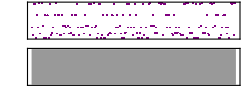

5symbol_GemGraph_substitution_level2_BlackKeys_1.mid

```mathematica
snd1=Sound[Table[SoundNote[RandomChoice[{"HighWoodblock","Snare","Sticks","SideStick","BassDrum","MidTom","LowBongo","LowTom","LowWoodblock"}],.24],{i,Length[PiDigits]}]]
Export["5symbol_GemGraph_substitution_level2_BlackKeys_1.mid",snd1]
```

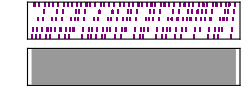

5symbol_GemGraph_substitution_level2_BlackKeys_2.mid

```mathematica
snd2=Sound[Table[SoundNote[PiDigits[[i]],.24,"Piano"],{i,Length[PiDigits]}]]
Export["5symbol_GemGraph_substitution_level2_BlackKeys_2.mid",snd2]
```

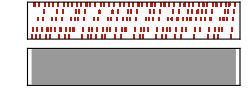

5symbol_GemGraph_substitution_level2_BlackKeys_2a.mid

```mathematica
snd2a=Sound[Table[SoundNote[PiDigits[[i]]-24,.24,"SynthBass2"],{i,Length[PiDigits]}]]
Export["5symbol_GemGraph_substitution_level2_BlackKeys_2a.mid",snd2a]
```

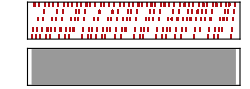

5symbol_GemGraph_substitution_level2_BlackKeys_10.mid

```mathematica
(* 8th notes*)
snd10=Sound[Table[SoundNote[PiDigits[[i]]+24,.24,"Flute"],{i,Length[PiDigits]}]]
Export["5symbol_GemGraph_substitution_level2_BlackKeys_10.mid",snd10]
```

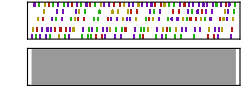

5symbol_GemGraph_substitution_level2_BlackKeys_3.mid

```mathematica
snd3=Sound[Table[SoundNote[PiDigits[[i]]-24,.24,RandomChoice[If[Mod[i,5]>0,{"Bass","ElectricBass","BassAndLead","PickedBass"},{"SynthBass2"}]]],{i,Length[PiDigits]}]]
Export["5symbol_GemGraph_substitution_level2_BlackKeys_3.mid",snd3]
```

```mathematica
w0={"Bass","ElectricBass","BassAndLead","PickedBass","SynthBass2"};
```

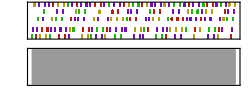

5symbol_GemGraph_substitution_level2_BlackKeys_3a.mid

```mathematica
snd3a=Sound[Table[SoundNote[PiDigits[[i]]-24,.24,w0[[1+Mod[i,5]]]],{i,Length[PiDigits]}]]
Export["5symbol_GemGraph_substitution_level2_BlackKeys_3a.mid",snd3a]
```

```mathematica
w1={"AltoSax","ElectricGuitar","Piano","Banjo","Whistle"};
```

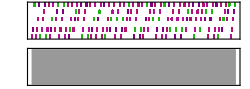

5symbol_GemGraph_substitution_level2_BlackKeys_4a.mid

```mathematica
snd4a=Sound[Table[SoundNote[PiDigits[[i]],.24,w1[[1+Mod[i,5]]]],{i,Length[PiDigits]}]]
Export["5symbol_GemGraph_substitution_level2_BlackKeys_4a.mid",snd4a]
```

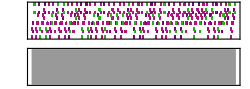

5symbol_GemGraph_substitution_level2_BlackKeys_4b.mid

```mathematica
snd4b=Sound[Table[SoundNote[{PiDigits[[i]],PiDigits[[i]]+3},.24,w1[[1+Mod[i,5]]]],{i,Length[PiDigits]}]]
Export["5symbol_GemGraph_substitution_level2_BlackKeys_4b.mid",snd4b]
```

```mathematica
snd5b=Sound[Table[SoundNote[{PiDigits[[i]],PiDigits[[i]]+3},.48,w1[[1+Mod[i,5]]]],{i,Length[PiDigits]}]]
Export["5symbol_GemGraph_substitution_level2_BlackKeys_5b.mid",snd5b]
(* quarter notes*)
```

-Graphics-

5symbol_GemGraph_substitution_level2_BlackKeys_5b.mid

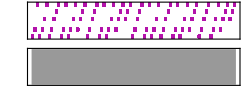

5symbol_GemGraph_substitution_level2_BlackKeys_5.mid

```mathematica
snd5=Sound[Table[SoundNote[PiDigits[[i]]+24,.48,"Tinklebell"],{i,Floor[Length[PiDigits]/2]}]]
Export["5symbol_GemGraph_substitution_level2_BlackKeys_5.mid",snd5]
```

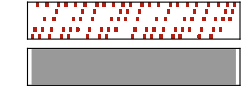

5symbol_GemGraph_substitution_level2_BlackKeys_6.mid

```mathematica
snd6=Sound[Table[SoundNote[PiDigits[[i]]-24,0.48,"SynthBass2"],{i,Floor[Length[PiDigits]/2]}]]
Export["5symbol_GemGraph_substitution_level2_BlackKeys_6.mid",snd6]
```

```mathematica
snd13=Sound[Table[SoundNote[PiDigits[[i]]+12,.20,"Piano"],{i,Length[PiDigits]}]]
Export["5symbol_GemGraph_substitution_level2_BlackKeys_13.mid",snd13]
```

-Graphics-

5symbol_GemGraph_substitution_level2_BlackKeys_13.mid

```mathematica
snd14=Sound[Table[SoundNote[PiDigits[[i]]-24,.20,"SynthBass2"],{i,Length[PiDigits]}]]
Export["5symbol_GemGraph_substitution_level2_BlackKeys_14.mid",snd14]
```

-Graphics-

5symbol_GemGraph_substitution_level2_BlackKeys_14.mid

```mathematica
wa={0.96,0.24,0.24,0.24,0.24,0.96,0.24,0.24,0.48,0.96,0.12,0.12,0.12,0.12};
```

```mathematica
Apply[Plus,wa]
```

5.28

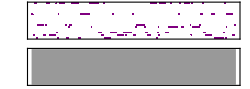

5symbol_GemGraph_substitution_level2_BlackKeys_8.mid

```mathematica
snd8=Sound[Table[SoundNote[RandomChoice[{"Snare","Sticks","BassDrum","Claves","MidTom","LowBongo","LowTom"}],wa[[1+Mod[i,Length[wa]]]]],{i,Floor[Length[PiDigits]/2]}]]
Export["5symbol_GemGraph_substitution_level2_BlackKeys_8.mid",snd8]
```

```mathematica
wb={4*0.24,0.24,0.24,0.24,0.24,0.48,0.48,0.48,0.48,0.24,0.24,0.24,0.24,0.48,0.48};
```

```mathematica
Apply[Plus,wb]
```

5.76

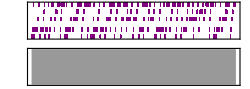

5symbol_GemGraph_substitution_level2_BlackKeys_4c.mid

```mathematica
snd4c=Sound[Table[SoundNote[PiDigits[[i]],wa[[1+Mod[i,Length[wa]]]],"Piano"],{i,Ceiling[Length[PiDigits]]}]]
Export["5symbol_GemGraph_substitution_level2_BlackKeys_4c.mid",snd4c]
```

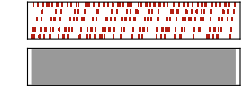

E5symbol_GemGraph_substitution_level2_BlackKeys_5c.mid

```mathematica
snd5c=Sound[Table[SoundNote[PiDigits[[i]]-24,wb[[1+Mod[i,Length[wb]]]],"SynthBass2"],{i,Ceiling[Length[PiDigits]]}]]
Export["E5symbol_GemGraph_substitution_level2_BlackKeys_5c.mid",snd5c]
```

```mathematica
Clear[wa,wb]
```

```mathematica
wa={0.12,0.12,0.12,0.12,0.24,0.24,0.48,0.48,0.24,0.24,0.24,0.24};
```

```mathematica
Apply[Plus,wa]
```

2.88

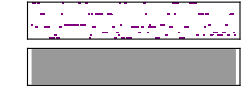

5symbol_GemGraph_substitution_level2_BlackKeys_9.mid

```mathematica
snd9=Sound[Table[SoundNote[RandomChoice[{"Snare","Sticks","BassDrum","Claves","MidTom","LowBongo","LowTom"}],wa[[1+Mod[i,Length[wa]]]]],{i,Floor[Length[PiDigits]/2]}]]
Export["5symbol_GemGraph_substitution_level2_BlackKeys_9.mid",snd9]
```

```mathematica
wb={0.24,0.24,0.24,0.24,0.24,0.12,0.12,0.12,0.12,0.48,0.72,0.12,0.12,0.12,0.12};
```

```mathematica
Apply[Plus,wb]
```

3.36

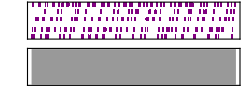

Edgar_substitution_4symbols_BlackKeys_level3_4d.mid

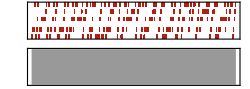

5symbol_GemGraph_substitution_level2_BlackKeys_5d.mid

```mathematica
snd4d=Sound[Table[SoundNote[PiDigits[[i]],wa[[1+Mod[i,Length[wa]]]],"Piano"],{i,Ceiling[Length[PiDigits]]}]]
Export["Edgar_substitution_4symbols_BlackKeys_level3_4d.mid",snd4d]
snd5d=Sound[Table[SoundNote[PiDigits[[i]]-24,wb[[1+Mod[i,Length[wb]]]],"SynthBass2"],{i,Ceiling[Length[PiDigits]]}]]
Export["5symbol_GemGraph_substitution_level2_BlackKeys_5d.mid",snd5d]
```

```mathematica
wc={4*0.24,0.24,0.24,0.24,0.24,4*0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,2*0.48,4*0.24,0.24,0.24,0.24,0.24,4*0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,2*0.48};
```

```mathematica
Apply[Plus,wc]
```

13.44

```mathematica
w1={None,"Piano",None,"Piano",None,"Piano",None,"Piano",None,"Piano",None,"Piano",None,"Piano"};
```

```mathematica
snd4f=Sound[Table[SoundNote[{PiDigits[[i]]-5,PiDigits[[i]],PiDigits[[i]]+3},wc[[1+Mod[i,Length[wc]]]],w1[[1+Mod[i,8]]]],{i,Ceiling[Length[PiDigits]]/8}]]
Export["5symbol_GemGraph_substitution_level2_BlackKeys_4f.mid",snd4f]
```

Sound[{SoundNote[{-4,1,4},0.24,Piano],SoundNote[{-2,3,6},0.24,None],SoundNote[{5,10,13},0.24,Piano],SoundNote[{-4,1,4},0.24,None],SoundNote[{-2,3,6},0.96,Piano],SoundNote[{1,6,9},0.24,None],SoundNote[{5,10,13},0.24,Piano],SoundNote[{-4,1,4},0.24,None],SoundNote[{-2,3,6},0.24,Piano],SoundNote[{1,6,9},0.24,None],SoundNote[{3,8,11},0.24,Piano],SoundNote[{5,10,13},0.24,None],SoundNote[{-4,1,4},0.24,Piano],SoundNote[{-2,3,6},0.24,None],SoundNote[{5,10,13},0.24,Piano],SoundNote[{-4,1,4},0.24,None],SoundNote[{-2,3,6},0.24,Piano],SoundNote[{1,6,9},0.96,None],SoundNote[{5,10,13},0.96,Piano],SoundNote[{-2,3,6},0.24,None],SoundNote[{1,6,9},0.24,Piano]}]

SoundNote::invinst: "None" is not a valid style specification.

General::stop: Further output of SoundNote::invinst will be suppressed during this calculation.

5symbol_GemGraph_substitution_level2_BlackKeys_4f.mid

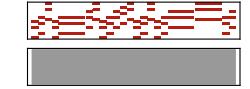

5symbol_GemGraph_substitution_level2_BlackKeys_5f.mid

```mathematica
snd5f=Sound[Table[SoundNote[{PiDigits[[i]]-5-12,PiDigits[[i]]-12,PiDigits[[i]]+3-12},wc[[1+Mod[i,Length[wc]]]],"SynthBass2"],{i,Ceiling[Length[PiDigits]]/8}]]
Export["5symbol_GemGraph_substitution_level2_BlackKeys_5f.mid",snd5f]
```

```mathematica
(*end*)
```